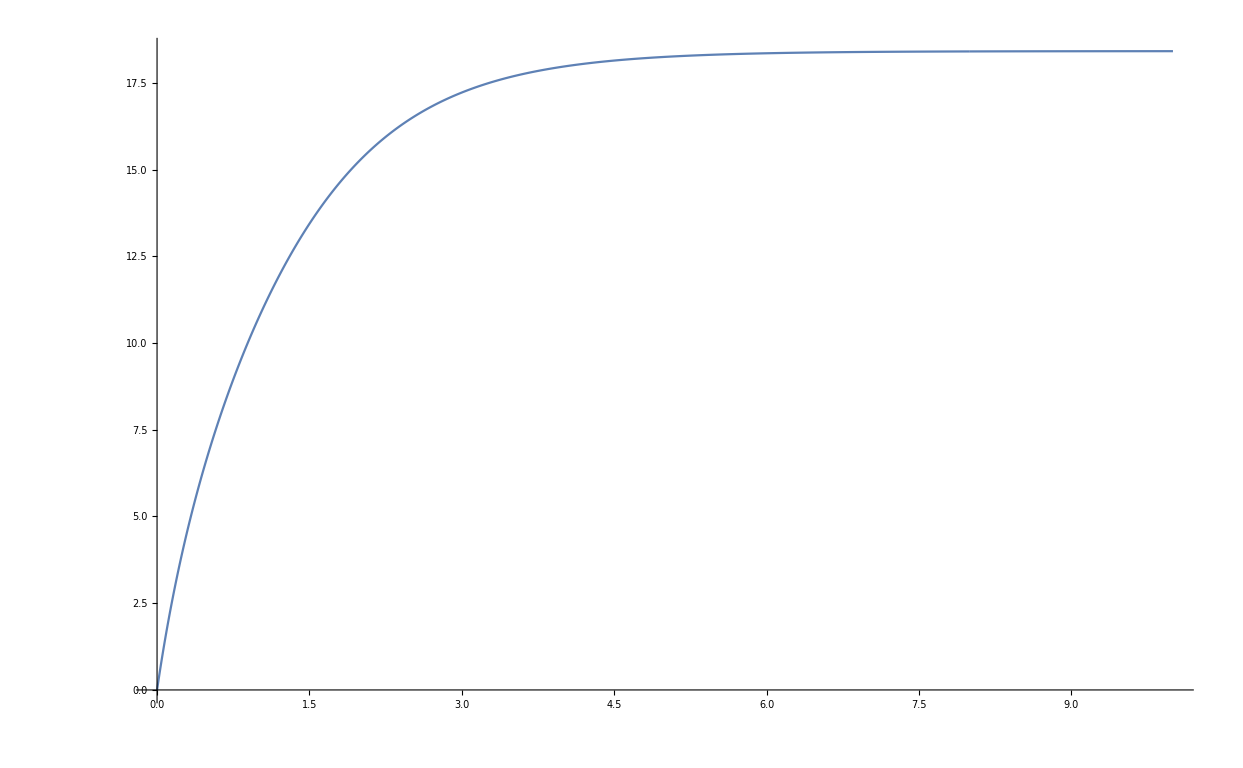

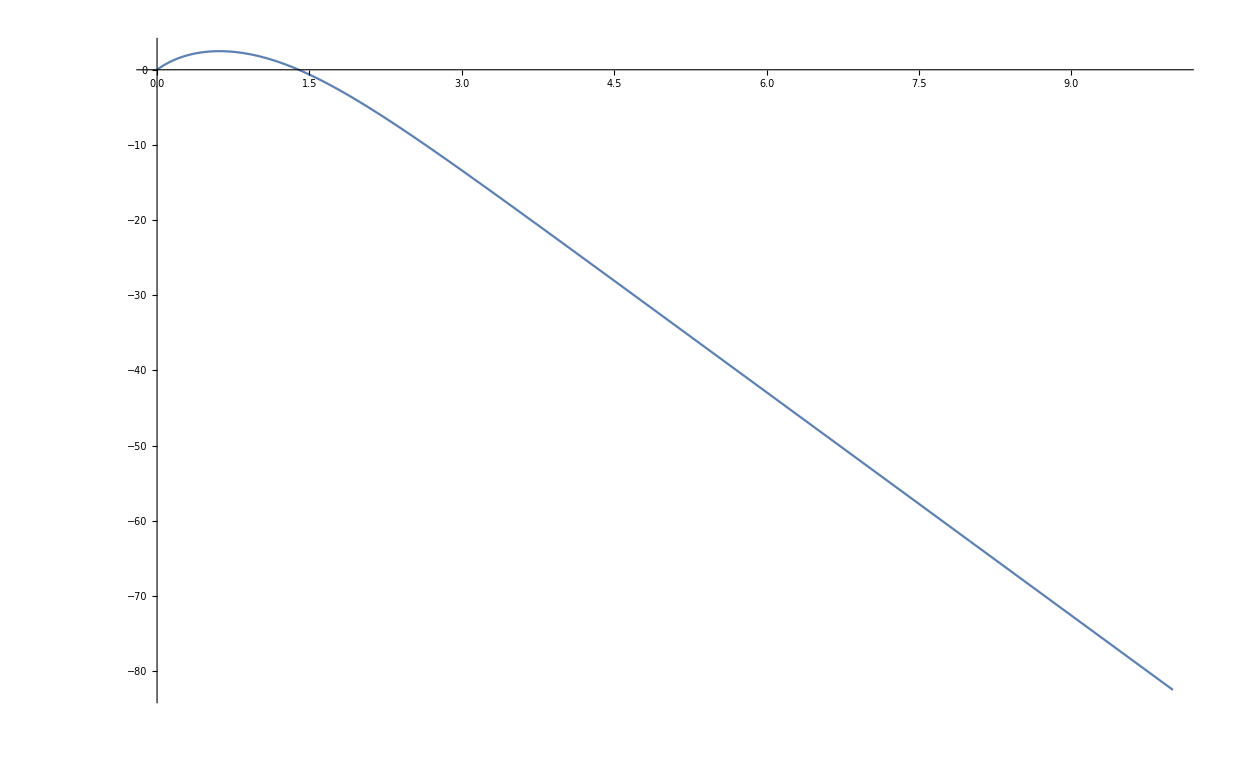

```mathematica
RK[f_,t_,x_,h_,n_]:=(*adding N[,30] makes our calculation more precise.But we need to take out 1. in places*)Module[{i,s=t,k1,k2,k3,k4,y=x,h2=N[h/2,30]},For[i=1,i≤n,i++,k1=h*f[s,y];
s=s+h2;
k2=h*f[s,y+k1/2];
k3=h*f[s,y+k2/2];
s=s+h2;
k4=h*f[s,y+k3];
y=y+(k1+2 k2+2 k3+k4)/6];
y];

(*g[t_,x_]:={x[[2]],((-9.8/0.6)*Sin[x[[1]]])};*)

g[t_,x_]:={x[[2]],-(0.1)*x[[2]]*(Sqrt[(x[[2]]^2)+(x[[4]]^2)]),x[[4]],-9.8-(0.1)*x[[4]]*(Sqrt[(x[[2]]^2)+(x[[4]]^2)])};

(*used for example 1 in notes*)
(*tf=1.;*)
(*n=100;*)
(*used for example 2 in notes*)
a=20;
dt=.001;(*if we make larger steps then we will see the plot has kinks,not smooth*)n=10;
x={0.,20.,0.,10.};

(*we have solved problems with RK Order 4 before but here we first converted higher order derivatives so we could work with them*)
(*example 1 in notes*)
(*RK[g,0.,{1.,0.},tf/n,n]-{Cos[tf],-Sin[tf]}(*subtract for error*)*)

(*example 2 in notes-pendulum*)
(*RK[g,0.,{0,a},tf/n,n]*)

(*we will make a list of data so we can plot*)
(*a lot of solvers work like this by making a list then we can interpolate on this say with splines*)
lst={};
lst2={};
For[t=0.,t<10,t=t+dt,lst=Append[lst,{t,x[[1]]}];
lst2=Append[lst2,{t,x[[3]]}];
x=RK[g,t,x,dt/n,n]];

ListPlot[lst,Joined->True]
ListPlot[lst2,Joined->True]
```

```mathematica
t=.6;(*near first 0*)n=100;
g[t_,x_]:={x[[2]],-(0.1)*x[[2]]*(Sqrt[(x[[2]]^2)+(x[[4]]^2)]),x[[4]],-9.8-(0.1)*x[[4]]*(Sqrt[(x[[2]]^2)+(x[[4]]^2)])};
x={0.,20.,0.,10.};
For[i=0,i<5,i++,x=RK[g,0,{0.,20.,0.,10.},t/n,n];(*flip a and 0*)t=t-x[[4]]/(-9.8-(0.1)*x[[4]]*(Sqrt[(x[[2]]^2)+(x[[4]]^2)]));(*flip x1,x2*)Print[t,"  ",x[[3]]]]
t=1.3;(*near first 0*)n=200;
For[i=0,i<5,i++,x=RK[g,0,{0.,20.,0.,10.},t/n,n];(*flip a and 0*)t=t-x[[3]]/x[[4]];(*flip x1,x2*)Print[t,"  ",x[[1]]]]
```

0.734191  3.22618

0.755279  3.34609

0.755706  3.34837

0.755706  3.34837

0.755706  3.34837

1.72637  17.1218

1.64125  20.6816

1.63805  20.0252

1.63805  20.

1.63805  20.

```mathematica
RK[f_,t_,x_,h_,n_]:=(*adding N[,30] makes our calculation more precise.But we need to take out 1. in places*)Module[{i,s=t,k1,k2,k3,k4,y=x,h2=N[h/2,30]},For[i=1,i≤n,i++,k1=h*f[y];
k2=h*f[y+k1/2];
k3=h*f[y+k2/2];k4=h*f[y+k3];
y=y+(k1+2 k2+2 k3+k4)/6];
y];(*secant method*)f[k_]:=Module[{x},air=k;
g[x_]:={x[[2]],-air*x[[2]]*(x[[2]]^2+x[[4]]^2)^(1/2),x[[4]],-9.8-(air*x[[4]]) (x[[2]]^2+x[[4]]^2)^(1/2)};
t=1.3;(*near maximum*)n=1600;(*needs to be larger.t for max is about 3 time t for min,to keep same step size need to make larger*)For[j=0,j<7,j++,x=RK[g,0.,{0.,20.,0.,10.},t/n,n];
t=t-x[[3]]/x[[4]];];
Return[x[[1]]];] (*Plot[f[x],{x,-2,2}]*)

y=.1;
yo=.05;
For[i=2,i<10,i++,fy=f[y];
fyo=f[yo];
yn=y-(fy-20) ((y-yo)/(fy-fyo));
Print["i: ",i," k: ",yn," landed at: ",fy];
yo=y;
y=yn;];
```

i: 2 k: 0.03911 landed at: 12.9458

i: 3 k: 0.0463971 landed at: 20.959

i: 4 k: 0.0436213 landed at: 19.4099

i: 5 k: 0.043459 landed at: 19.9674

i: 6 k: 0.0434646 landed at: 20.0012

i: 7 k: 0.0434646 landed at: 20.

i: 8 k: 0.0434646 landed at: 20.

i: 9 k: 0.0434646 landed at: 20.